```mathematica
c=Sqrt[0.2641]
Needs["PlotLegends`"]
a=10
b=1
v=10
f[x_]:=c Sqrt[x-v]Sin[c a Sqrt[x]]Cos[c b Sqrt[x-v]]+c Sqrt[x]Cos[c a Sqrt[x]]Sin[c b Sqrt[x-v]]
g[x_]:=c Sqrt[v-x]Sin[c a Sqrt[x]]Cosh[c b Sqrt[b-x]]+c Sqrt[x]Cos[c a Sqrt[x]]Sinh[c b Sqrt[v-x]]
```

0.513907

10

1

10

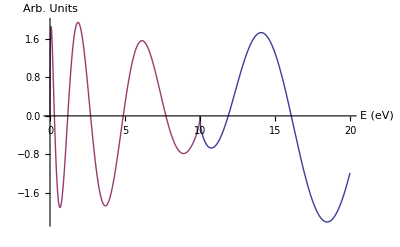

```mathematica
Plot[{f[x],g[x]},{x,0,20},AxesLabel->{"E (eV)","Arb. Units"}]
```